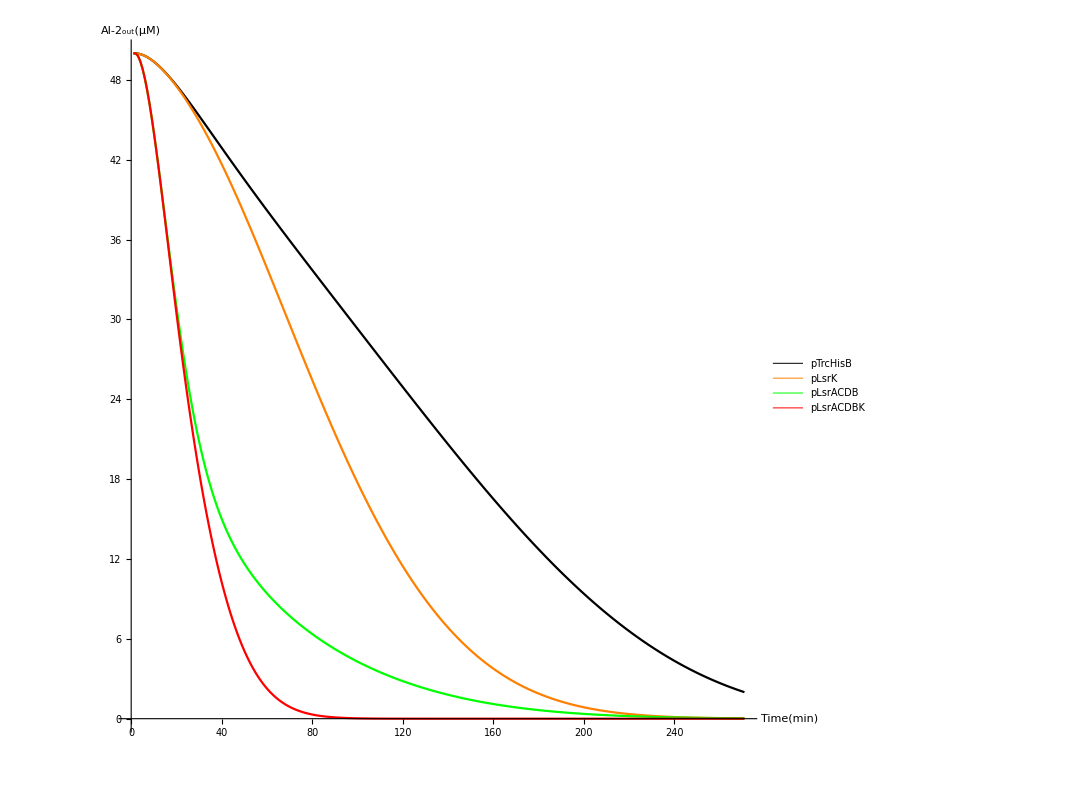

```mathematica
Serialize[f_,imin_, imax_, di_:1]:=Table[f[t],{t,imin, imax, di}]
Mark[text_, color_:Blue,size_:Large]:=Style[text, color, size]
LineStyle[color_:Black, thickness_:0.002]:=Directive[color, Thickness[thickness]]
(*Caution! The unit of time should be dt, though its default value is 1 minute.*)
Options[Consumer]={kin->0.008,kout->0.045,kp->0.006,Ki->0.9,Knat->0.1,kd->0.02,μ->0.0056,μT->0.0044,tmax->270,dt->1,IPTGK-> 0,IPTGACDB->0,iOD600-> 0.5,iLsrΚ->0,iLsrACDB->0,iAI2in-> 0,iAI2out-> 50,index->5};
Consumer[OptionsPattern[]]:=
Module[{kin=OptionValue[kin],kout=OptionValue[kout],kp=OptionValue[kp],Ki=OptionValue[Ki],Knat=OptionValue[Knat],kd=OptionValue[kd],μ=OptionValue[μ],μT=OptionValue[μT],tmax=OptionValue[tmax],dt=OptionValue[dt],IPTGK=OptionValue[IPTGK],IPTGACDB=OptionValue[IPTGACDB],LsrΚ,LsrACDB,AI2in,AI2out,index=OptionValue[index],n},
If[IPTGACDB==1,μ=μT];
OD600=(0.5 ⅇ^(μ #))&;
LsrΚ[0]=OptionValue[iLsrΚ];
LsrACDB[0]=OptionValue[iLsrACDB];
AI2in[0]=OptionValue[iAI2in];
AI2out[0]=OptionValue[iAI2out];
n=Floor[tmax/dt];
Do[LsrΚ[i]=LsrΚ[i-1]+((Knat+Ki*IPTGK)*OD600[i-1]-kd*LsrΚ[i-1])*dt;LsrACDB[i]=LsrACDB[i-1]+((Knat+Ki*IPTGACDB)*OD600[i-1]-kd*LsrACDB[i-1])*dt;AI2in[i]=AI2in[i-1]+(kin*LsrACDB[i-1]*AI2out[i-1]-kout*AI2in[i-1]-kp*LsrΚ[i-1]*AI2in[i-1])*dt;AI2out[i]=AI2out[i-1]+(-kin*LsrACDB[i-1]*AI2out[i-1]+kout*AI2in[i-1])*dt
,{i,n}];
{Serialize[OD600,0,n],Serialize[LsrΚ,0,n],Serialize[LsrACDB,0,n],Serialize[AI2in,0,n],Serialize[AI2out,0,n]}[[index]]]
ListPlot[{Consumer[],Consumer[IPTGK->1],Consumer[IPTGACDB->1],Consumer[IPTGK->1,IPTGACDB->1]}, Joined->True,PlotStyle->{LineStyle[Black],LineStyle[Orange],LineStyle[Green],LineStyle[Red]},PlotLegends->Placed[{Mark["pTrcHisB",Black],Mark["pLsrK",Orange],Mark["pLsrACDB",Green],Mark["pLsrACDBK",Red]},{0.8,0.8}],AxesLabel->{Mark["Time(min)"],Mark["AI-2_out(μM)"]},AxesStyle->Directive[Large,Blue],ImageSize->800,AspectRatio->1]
```